# Lab 4 - Series Expansions

```mathematica
Needs["PlotLegends`"]
dir = NotebookDirectory[];
SetDirectory[dir];
```

Series Sin and Cosine around x=0 out to n terms.

```mathematica
SerCos[x_,n_] := Normal[Series[Cos[a], {a,0,n}]] /. a->x
```

```mathematica
SerSin[x_,n_] := Normal[Series[Sin[a], {a,0,n}]] /. a->x
```

Evaluate the difference between SerSin and Sin.

```mathematica
serSinDiff[x_, n_] := SerSin[x,n] - Sin[x]
```

```mathematica
data = Table[serSinDiff[x,n], {n, 5,11,2}]
```

{x-x^3/6+x^5/120-Sin[x],x-x^3/6+x^5/120-x^7/5040-Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880-Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800-Sin[x]}

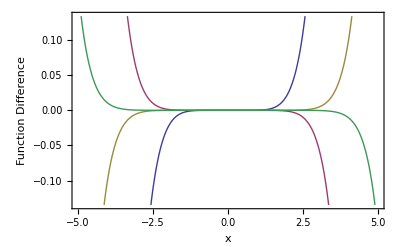

```mathematica
graph = Plot[{data[[1]],data[[2]],data[[3]],data[[4]]},{x,-5,5}, Frame -> True, FrameLabel->{{"Function Difference", ""},{"x", "SerSin[x,n] - Sin[x]"}},PlotLegend->{"n=5","n=7","n=9","n=11"},LegendPosition->{.85,-0.4}, PlotStyle-> Thick]
```

```mathematica
Export["difference.png", graph]
```

difference.png